Define the model’s equations

```mathematica
dS=-β S[t] II[t];
dI=β S[t] II[t] - r II[t];
dR = r II[t];
```

Model parameters

```mathematica
parms = {β-> 10^-3, r->0.1};
inits={S0->499, I0->1, R0->0};
tfinal=100;
```

Define the system of equations for NDSolve

```mathematica
eqs = {S'[t]==dS, II'[t]==dI, R'[t]==dR,S[0]==S0,II[0]==I0,R[0]==R0}/.inits/.parms
```

{S'[t]==-(II[t] S[t])/1000,II'[t]==-0.1 II[t]+(II[t] S[t])/1000,R'[t]==0.1 II[t],S[0]==499,II[0]==1,R[0]==0}

```mathematica
vars= {S, II, R};
```

Numerically solve the system

```mathematica
sol=NDSolve[eqs, vars, {t,0,tfinal}]
```

{{S→InterpolatingFunction[…],II→InterpolatingFunction[…],R→InterpolatingFunction[…]}}

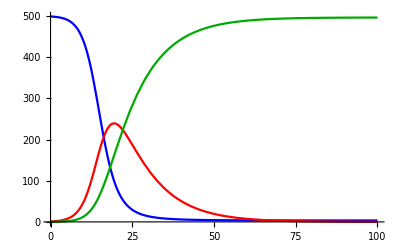

```mathematica
Plot[{S[t]/.sol,II[t]/.sol,R[t]/.sol},{t,0,tfinal},PlotStyle->{Blue, Red, Darker[Green]}]
```